#### 表达式的存储

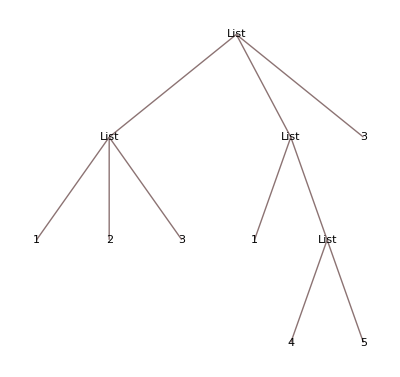

```mathematica
list1 = {{1,2,3},{1,{4,5}},3};(*表达式其实是以树形式存储的*)
{{1,2,3},{1,{4,5}},3}//TreeForm
```

#### Part函数

```mathematica
list1⟦2,1⟧(*取list1的第二个元素的第1个元素*)
```

1

```mathematica
(*挨个提取第一层的第一个元素*)
list1⟦All,1⟧
```

Part::partd: 部分指定 {{1,2,3},{1,{4,5}},3}⟦All,1⟧ 比对象深度更长.

{{1,2,3},{1,{4,5}},3}⟦All,1⟧

```mathematica
Head[list1](*上图的树根*)
```

List

```mathematica
(*Apply 或者@@ 其实是替换表达式头部的一个操作*)
?Apply
```

Apply[f,expr] 或 f@@expr 用 f 替换 expr 的头部. 
Apply[f,expr,{1}] 或 f@@@expr 用 f 替换 expr 的第 1 层的头部.
Apply[f,expr,levelspec] 替换 expr 中使用 levelspec 指定的部分的头部. 
Apply[f] 表示 Apply 的运算符形式，它可以应用于表达式.

```mathematica
(*@@@其实是替换树的第一层*)
```